```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
(* Define an inflationary potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^2;
vp[x_]=v'[x];
ni = 80; (* initial value f n for integration *)
nf = -1.3; (* final value of n for integration *)
ni2 = 70;
nf2 = 0;
n1guess = -1.1;
```

```mathematica
(* Define the hubble parameter *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
```

```mathematica
(* Find the slow roll initial conditions *)
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
ϕi1= t/.Last[NSolve[ni==f[t],t]];
Print["ϕi1 = ",ϕi1];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
Print["ϕpi1 = ",ϕpi1];
```

ϕi1 = 17.9444

ϕpi1 = 0.111456

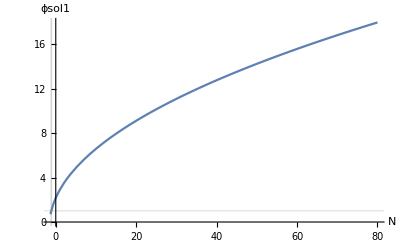

```mathematica
(* Solve the Klein-Gordon equation for ϕ[n] *)
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
p1=Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol1"},GridLines->{{-1,-1.2},{1}}]
```

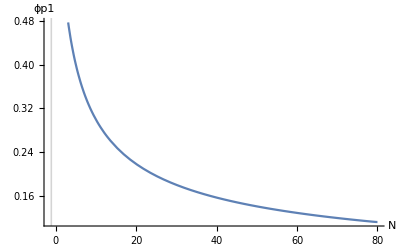

```mathematica
(* Find ϵ1 *)
ϕ1p[n_] = D[ϕ[n],n]/.ϕsol1;
Plot[Evaluate[ϕ1p[n]],{n,nf,ni},AxesLabel->{N,"ϕp1"},GridLines->{{-1,-1.2},{1}}]
```

At n = 0, ϵ1 = 0.342302

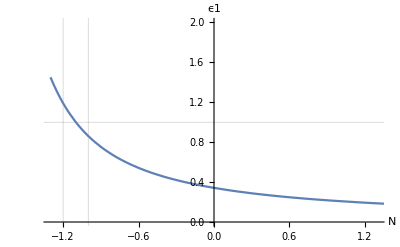

```mathematica
h1sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ1p[n]^2)/.ϕsol1;
ϵ1[n_] = Evaluate[3*ϕ1p[n]^2/(ϕ1p[n]^2+2*v[ϕ[n]]/h1sq[n])/.ϕsol1];
Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]];
Plot[ϵ1[n],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]
```

```mathematica
(* Solve for where ϵ1[n]==1 *)
(* Evaluate[n/.Last@NSolve[ϵ1[n]==1,n]] *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]];
```

At n1 = -1.09848, ϵ1 = 1.

ϕf2 = 1.00934

ϕpf2 = 1.41421

ϕi2 = 16.6644

ϕpi2 = 0.11973

1.

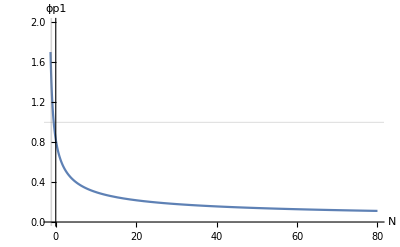

ϕpi2 = 0.11973

ϕi2 = 16.6644

ϕpf2 = 1.41421

ϕf2 = 1.00934

ϕi2 = 17.9444

```mathematica
ϕf2 = ϕ[n1]/.ϕsol1;
Print["ϕf2 = ",ϕf2];
ϕpf2 = D[ϕ[n],n]/.ϕsol1/.n->n1;
Print["ϕpf2 = ",ϕpf2];
(* ϕpi2 = vp[ϕi2]/v[ϕi2] ; 
Print["ϕpi2 = ",ϕpi2]; *)
ϕi2 = ϕ[ni2+n1]/.ϕsol1;
Print["ϕi2 = ",ϕi2];
ϕpi2 = D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1);
Print["ϕpi2 = ",ϕpi2];
(3/2)*ϕpf2^2*h1sq[n1]/((1/2)*ϕpf2^2*h1sq[n1]+v[ϕf2])
Plot[Evaluate[D[ϕ[n],n]/.ϕsol1/.n->nx],{nx,nf,ni},AxesLabel->{N,"ϕp1"},PlotRange->{{nf,ni},{0,2}},GridLines->{{-1,-1.2},{1}}]
```

```mathematica
hsq[0]
```

ϕ[0]^2/(3-1/2 ϕ'[0]^2)

16.9254

InterpolatingFunction::dmval: Input value {80} lies outside the range of data in the interpolating function. Extrapolation will be used.

17.8617

InterpolatingFunction::dmval: Input value {-1.09705} lies outside the range of data in the interpolating function. Extrapolation will be used.

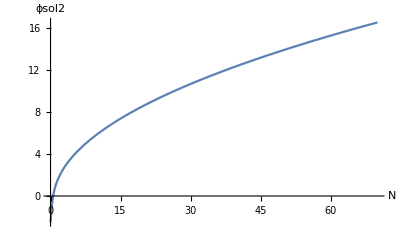

```mathematica
(* ϕsol2 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[nf2]==ϕf2,ϕ[ni2]==ϕi2},ϕ,{n,nf2,ni2},InterpolationOrder->All]; *)
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
ϕsol2 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni2]==ϕi2,ϕ'[ni2]==ϕpi2},ϕ,{n,ni2,nf2},InterpolationOrder->All];
ϕ[n]/.ϕsol1/.n->(ni2-n1)
ϕ[n]/.ϕsol2/.n->ni
p2=Plot[Evaluate[ϕ[n+n1]/.ϕsol2],{n,nf2,ni2},AxesLabel->{N,"ϕsol2"}]
```

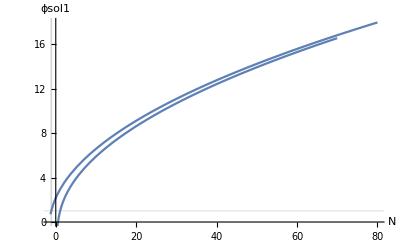

```mathematica
Show[p1,p2]
```

0.118781

InterpolatingFunction::dmval: Input value {-1.19834} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

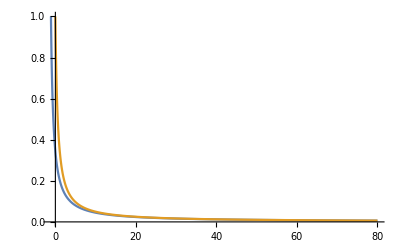

At n = 0, ϵ1 = 1.

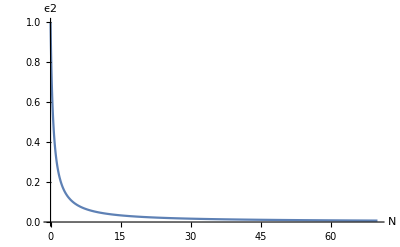

```mathematica
(* Find ϵ2 *)
ϕ1p[n_] = D[ϕ[n],n]/.ϕsol1;
ϕ2p[n_] = D[ϕ[n],n]/.ϕsol2;
h1sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ1p[n]^2)/.ϕsol1;
h2sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ2p[n]^2)/.ϕsol2;
ϵ2[n_] = Evaluate[3*ϕ2p[n]^2/(ϕ2p[n]^2+2*v[ϕ[n]]/h2sq[n])/.ϕsol2];
ϵ2[n]/.n->4
Plot[{ϵ1[n],ϵ2[n]},{n,-1.2,80},PlotRange->{{-1.2,80},{0,1}}]
Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]];
Plot[ϵ2[n],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]
```

ns[60] = 0.966592

r[60] = 0.133817

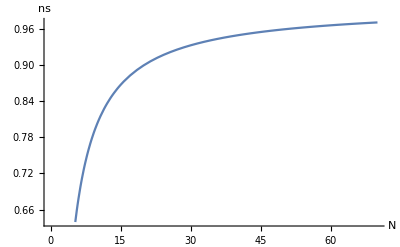

```mathematica
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
Print["ns[60] = ",ns[n]/.{n->60}];
r[n_] := 16*(ϵ2[n]/.{n->60});
Print["r[60] = ",r[n]/.{n->60}];
Plot[Evaluate[ns[n]],{n,ni2,nf2},AxesLabel->{N,ns}]
```